# Patch weight convergence test

### To ensure that our assumptions about how patch size relates to the values of patch weights, we will do some simulations: - for uniform weights, draw 10,000 patches with weights - sum each set of patch weights - check gross and average deviation, via or as n increases, we expect that average deviation will go to zero for [values of q]: - same process as constant weights above, but for 4 separate values of q

## Uniform weights

```mathematica
SeedRandom[123]; (* set seed so stuff is reproducible *)
(* number of repetitions per n *)
numReps = 1000;

(* geometric range of n values *)
nValues = Range[1000, 10000000, 100000];
Length[nValues]
(* simulate for each n *)
results = ParallelTable[
  Module[{samples, sums, sqDev, absDev},
    
    (* draw numReps samples of n uniform weights on (0, 2/n) *)
    samples = Table[
      Total@RandomReal[{0, 2/n}, n],
      {numReps}
    ];
    
    (* compute deviance metrics *)
    sqDev = Mean[(# - 1)^2 & /@ samples];
    absDev = Mean[Abs[# - 1] & /@ samples];
    
    <|
      "n" -> n,
      "MeanSum" -> Mean[samples],
      "SquaredDeviance" -> sqDev,
      "AbsoluteDeviance" -> absDev
    |>
  ],
  {n, nValues}
];

(* convert to a dataset for inspection *)
devTable = Dataset[results]
```

100

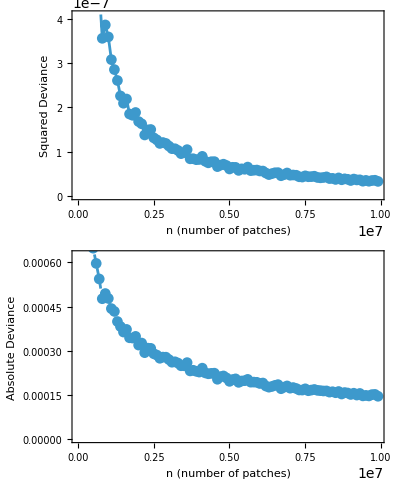

```mathematica
(* extract x and y values *)
squaredPoints = {#["n"], #["SquaredDeviance"]} & /@ results;
absolutePoints = {#["n"], #["AbsoluteDeviance"]} & /@ results;

(* top panel: squared deviance *)
sqPlot = ListPlot[
  squaredPoints,
  PlotStyle -> Automatic,
  Frame -> True,
  FrameLabel -> {"n (number of patches)", "Squared Deviance"},
  PlotMarkers -> Automatic,
  Joined -> True
];

(* bottom panel: absolute deviance *)
absPlot = ListPlot[
  absolutePoints,
  PlotStyle -> Dashed,
  Frame -> True,
  FrameLabel -> {"n (number of patches)", "Absolute Deviance"},
  PlotMarkers -> Automatic,
  Joined -> True
];

(* combine plots *)
GraphicsGrid[{{sqPlot}, {absPlot}}, Spacings -> {0, 2}]
```

## Uniform weights with q

```mathematica
(* number of repetitions *)
numReps = 1000;

(* geometric range of n values *)
nValues = Range[1000, 10000000, 100000];

(* main simulation loop *)
landscapeVarianceResults = ParallelTable[
  Module[{qVals, qResults},
 
	qVals  = {0, 1/(2 n), 1/n};          (* numeric values, depend on n *)
	qLbls  = {"0", "1/(2n)", "1/n"};     (* symbolic strings, never change *)

	qResults = MapThread[Module[{q = #2, label = #1, samples, sqDev, absDev},
     samples = Table[
       Total @ RandomReal[{1/n - q, 1/n + q}, n],
       {numReps}
     ];
     sqDev  = Mean[(# - 1)^2 & /@ samples];
     absDev = Mean[Abs[# - 1] & /@ samples];

     <|
       "n"               -> n,
       "qRaw"            -> q,          (* numeric 0, 1/(2 n), 1/n *)
       "qLabel"          -> label,      (* **fixed string** 0, 1/(2n), 1/n *)
       "MeanSum"         -> Mean[samples],
       "SquaredDeviance" -> sqDev,
       "AbsoluteDeviance"-> absDev
     |>
   ] &,
   {qLbls, qVals}                      (* thread label ↔ value *)
];
    qResults
  ],
  {n, nValues}
];


(* flatten results *)
landscapeVarianceResultsFlat = Flatten[landscapeVarianceResults, 1];
devDS = Dataset[landscapeVarianceResultsFlat];
```

```mathematica
devDS;
```

```mathematica
grouped = GroupBy[landscapeVarianceResultsFlat, #["qLabel"] &];

(* pick out the “1/(2n)” group, regardless of which n produced it *)
sqDevNCurve = {#["n"], #["SquaredDeviance"]} & /@ grouped["1/(2n)"]
```

{{1000,0.0000819801},{11000,7.02608×10^-6},{21000,3.87115×10^-6},{31000,2.61347×10^-6},{41000,2.12034×10^-6},{51000,1.52842×10^-6},{61000,1.48829×10^-6},{71000,1.17577×10^-6},{81000,1.09957×10^-6},{91000,9.48668×10^-7}}

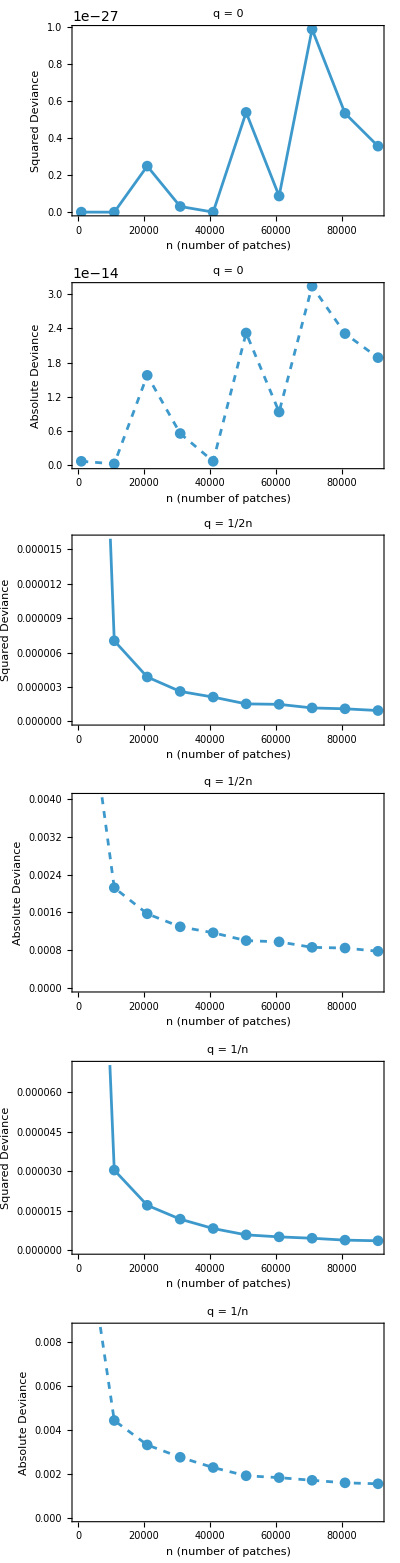

```mathematica
(* q = 0 *)
squaredPoints0 = {#["n"], #["SquaredDeviance"]} & /@ grouped["0"];
absolutePoints0 = {#["n"], #["AbsoluteDeviance"]} & /@ grouped["0"];

sqPlot0 = ListPlot[
  squaredPoints0,
  PlotStyle -> Automatic,
  Frame -> True,
  FrameLabel -> {"n (number of patches)", "Squared Deviance"},
  PlotLabel -> "q = 0",
  PlotMarkers -> Automatic,
  Joined -> True
];

absPlot0 = ListPlot[
  absolutePoints0,
  PlotStyle -> Dashed,
  Frame -> True,
  FrameLabel -> {"n (number of patches)", "Absolute Deviance"},
  PlotLabel -> "q = 0",
  PlotMarkers -> Automatic,
  Joined -> True
];

(* q = 1/2n *)
squaredPointsHalf = {#["n"], #["SquaredDeviance"]} & /@ grouped["1/(2n)"];
absolutePointsHalf = {#["n"], #["AbsoluteDeviance"]} & /@ grouped["1/(2n)"];

sqPlotHalf = ListPlot[
  squaredPointsHalf,
  PlotStyle -> Automatic,
  Frame -> True,
  FrameLabel -> {"n (number of patches)", "Squared Deviance"},
  PlotLabel -> "q = 1/2n",
  PlotMarkers -> Automatic,
  Joined -> True
];

absPlotHalf = ListPlot[
  absolutePointsHalf,
  PlotStyle -> Dashed,
  Frame -> True,
  FrameLabel -> {"n (number of patches)", "Absolute Deviance"},
  PlotLabel -> "q = 1/2n",
  PlotMarkers -> Automatic,
  Joined -> True
];

(* q = 1/n *)
squaredPoints1 = {#["n"], #["SquaredDeviance"]} & /@ grouped["1/n"];
absolutePoints1 = {#["n"], #["AbsoluteDeviance"]} & /@ grouped["1/n"];

sqPlot1 = ListPlot[
  squaredPoints1,
  PlotStyle -> Automatic,
  Frame -> True,
  FrameLabel -> {"n (number of patches)", "Squared Deviance"},
  PlotLabel -> "q = 1/n",
  PlotMarkers -> Automatic,
  Joined -> True
];

absPlot1 = ListPlot[
  absolutePoints1,
  PlotStyle -> Dashed,
  Frame -> True,
  FrameLabel -> {"n (number of patches)", "Absolute Deviance"},
  PlotLabel -> "q = 1/n",
  PlotMarkers -> Automatic,
  Joined -> True
];

(* stitch all 6 plots together *)
GraphicsGrid[
  {
    {sqPlot0},
    {absPlot0},
    {sqPlotHalf},
    {absPlotHalf},
    {sqPlot1},
    {absPlot1}
  },
  Spacings -> {0, 2}
]
```